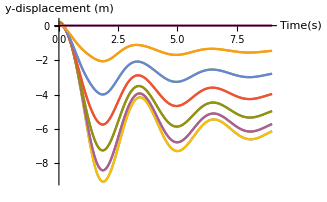
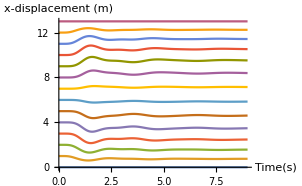

```mathematica
t0=9;P=14;lr=1;g=9.8;m=1;ks=100;kd=10;
eqns={Table[m*x[i]''[t]==-ks*(Sqrt[(x[i][t]-x[i-1][t])^2+(y[i][t]-y[i-1][t])^2]-lr)*(x[i][t]-x[i-1][t])/Sqrt[(x[i][t]-x[i-1][t])^2+(y[i][t]-y[i-1][t])^2]-ks*(Sqrt[(x[i][t]-x[i+1][t])^2+(y[i][t]-y[i+1][t])^2]-lr)*(x[i][t]-x[i+1][t])/Sqrt[(x[i][t]-x[i+1][t])^2+(y[i][t]-y[i+1][t])^2]-kd*(x[i]'[t]-x[i-1]'[t])-kd*(x[i]'[t]-x[i+1]'[t]),{i,2,P-1}],Table[m*y[i]''[t]==-ks*(Sqrt[(x[i][t]-x[i-1][t])^2+(y[i][t]-y[i-1][t])^2]-lr)*(y[i][t]-y[i-1][t])/Sqrt[(x[i][t]-x[i-1][t])^2+(y[i][t]-y[i-1][t])^2]-ks*(Sqrt[(x[i][t]-x[i+1][t])^2+(y[i][t]-y[i+1][t])^2]-lr)*(y[i][t]-y[i+1][t])/Sqrt[(x[i][t]-x[i+1][t])^2+(y[i][t]-y[i+1][t])^2]-kd*(y[i]'[t]-y[i-1]'[t])-kd*(y[i]'[t]-y[i+1]'[t])-m*g,{i,2,P-1}]};
ic1={Table[y[i]'[0]==0,{i,1,P}],Table[y[i][0]==0,{i,1,P}],Table[x[i][0]==lr*(i-1),{i,1,P}],Table[x[i]'[0]==0,{i,1,P}]};
ic2={{y[1]'[0]==0,y[2]'[0]==7.083974359,y[3]'[0]==12.99055944,y[4]'[0]==17.71975524,y[5]'[0]==21.27156177,y[6]'[0]==23.64597902,y[7]'[0]==24.84300699,
y[8]'[0]==24.84300699,y[9]'[0]==23.64597902,y[10]'[0]==21.27156177,y[11]'[0]==17.71975524,y[12]'[0]==12.99055944,y[13]'[0]==7.083974359,y[14]'[0]==0},Table[y[i][0]==0,{i,1,P}],Table[x[i][0]==lr*(i-1),{i,1,P}],Table[x[i]'[0]==0,{i,1,P}]};
ic3={Table[y[i]'[0]==0,{i,1,P}],{y[1][0]==0,y[2][0]==0.0384620,y[3][0]==0.0769230,y[4][0]==0.1153850,y[5][0]==0.1538460,y[6][0]==0.1923080,y[7][0]==.230769,
y[8][0]==0.230769,y[9][0]==0.1923080,y[10][0]==0.1538460,y[11][0]==0.1153850,y[12][0]==0.0769230,y[13][0]==0.0384620,y[14][0]==0},Table[x[i][0]==lr*(i-1),{i,1,P}],Table[x[i]'[0]==0,{i,1,P}]};
bc={x[P]''[t]==0,x[1]''[t]==0,y[P]''[t]==0,y[1]''[t]==0};

Y=NDSolveValue[{eqns,ic3,bc},Table[y[i][t],{i,1,P}],{t,0,t0}];X=NDSolveValue[{eqns,ic3,bc},Table[x[i][t],{i,1,P}],{t,0,t0}];
{Plot[Y,{t,0,t0},PlotRange->All,AxesLabel->{"Time(s)","y-displacement (m)"}],Plot[X,{t,0,t0},PlotRange->All,AxesLabel->{"Time(s)","x-displacement (m)"}]}
```

```mathematica
10
```

10

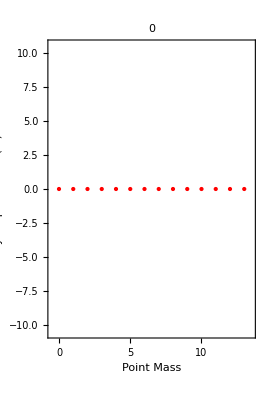
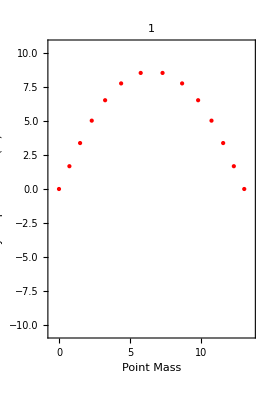
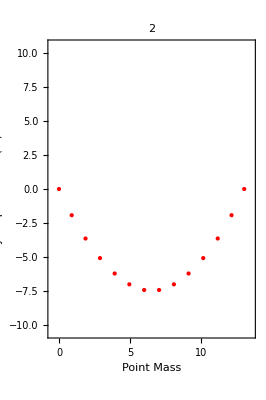
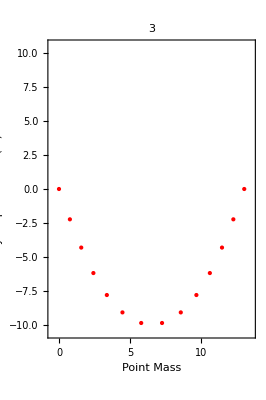
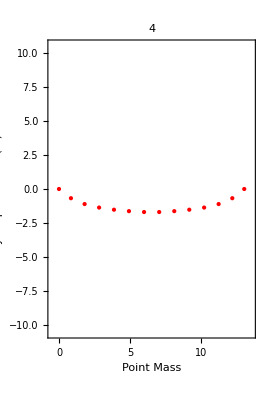
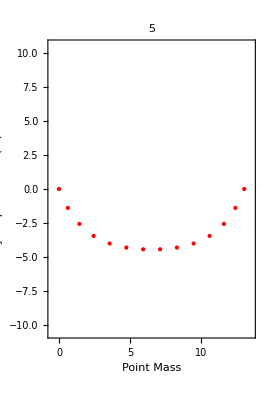
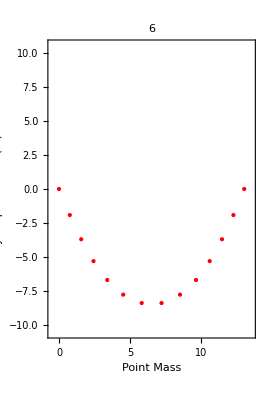
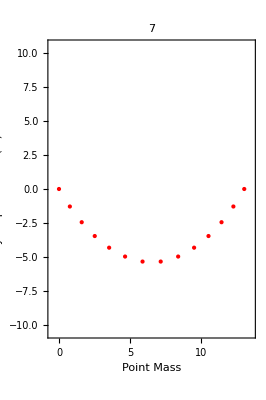

```mathematica
Table[Graphics[{PointSize[Medium],Red,Point[NDSolveValue[{eqns,ic2,bc},Table[{x[i][tn],y[i][tn]},{i,1,P}],{t,0,tn}]]},Frame->True,FrameLabel->{"Point Mass","y-Displacement  (m)"},PlotLabel->tn,PlotRange->{{-.5,13.5},{-10.5,10.5}}],{tn,0,t0,1}]
```

```mathematica
z
```

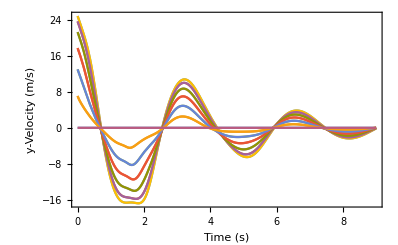
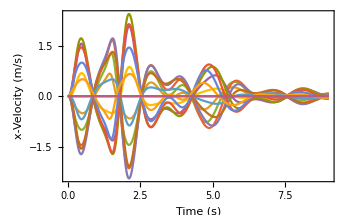

```mathematica
VY=NDSolveValue[{eqns,ic2,bc},Table[y[i]'[t],{i,1,P}],{t,0,t0}];VX=NDSolveValue[{eqns,ic2,bc},Table[x[i]'[t],{i,1,P}],{t,0,t0}];
{Plot[VY,{t,0,t0},Frame->True,FrameLabel->{"Time  (s)","y-Velocity  (m/s)"},PlotRange->All],Plot[VX,{t,0,t0},PlotRange->All,Frame->True,FrameLabel->{"Time  (s)","x-Velocity  (m/s)"}]}
```